## Асимптотика волновой функции для 1D кулона

z - заряд остова
k = √(2 I_p)
ψ'' + (2 z/x-k^2)ψ = 0

```mathematica
ShrodingerEq= ψ''[x]+(2 z/x-k^2)ψ[x]==0
```

(-k^2+(2 z)/x) ψ[x]+ψ''[x]==0

Выделяем экспоненту и степенную зависимость:

```mathematica
ψ[x_] := x^a ⅇ^(-k x)
```

```mathematica
Simplify[ShrodingerEq]
```

ⅇ^(-k x) x^(-1+a) (a-a^2+2 a k x-2 x z)==0

Скобка должна равняться нулю

```mathematica
aEq[a_] = a-a^2+2 a k x-2 x z
```

a-a^2+2 a k x-2 x z

На больших расстояниях доминимует член
2a k x - 2 z x
Коротый зануляется при 
a = z/k

Получаем:

```mathematica
ψ[x_] := x^(z/k)ⅇ^(-k x)
```

## Квазиклассика

Применимость квазиклассики вблизи нуля

```mathematica
p[x_]:=√((2z)/(√(x^2+a^2))-k^2)
VkbApplty= D[1/p[x], x]
```

(x z)/((a^2+x^2)^(3/2) (-k^2+(2 z)/(√(a^2+x^2)))^(3/2))

Модуль импульса под барьером :

```mathematica
pabs[x_] := √(k^2-(2z)/x-2e x)
```

Разложение в ряд:

```mathematica
pabsSeries = Series[ √(k^2-ϵ-2e x), {ϵ, 0, 2}] /. ϵ-> (2z)/x//Simplify
```

SeriesData::sdatv: First argument (2 z)/x is not a valid variable.

√(k^2-2 e x)-(2 z)/(2 √(k^2-2 e x) x)-((2 z)/x)^2/(8 (k^2-2 e x)^(3/2))+O[(2 z)/x]^3

Интегрирование I1:

```mathematica
I1 =-2* Integrate[√(k^2-2 e x), x]
```

(2 (k^2-2 e x)^(3/2))/(3 e)

Интегрирование I1 :

```mathematica
I2 = -2*Integrate[-(2 z)/(2 √(k^2-2 e x) x), x]//TrigToExp
```

(2 z Log[1-(√(k^2-2 e x))/k])/k-(2 z Log[1+(√(k^2-2 e x))/k])/k

Интегрирование I3

```mathematica
I3= -2*Integrate[-((2 z)/x)^2/(8 (k^2-2 e x)^(3/2)), x]
```

(4 e z^2 Hypergeometric2F1[-1/2,2,1/2,1-(2 e x)/k^2])/(k^4 √(k^2-2 e x))

## Квазиклассика вбизи нуля

```mathematica
$Assumptions={z>0,a>0, k>0, e>0};
```

Потенциал

```mathematica
V[x_]:=-z/(√(x^2+a^2))
```

Разложение потенциала в ряд

```mathematica
Series[V[x], {x,0, 4}]//Simplify
```

-z/a+(z x^2)/(2 a^3)-(3 z x^4)/(8 a^5)+O[x]^5

Решение ур. Шредингера в атомном потенциале в виде ряда

```mathematica
PsiSeriesZero[x_, z_, k_, a_]=AsymptoticDSolveValue[{y''[x]+((2z)/(√(x^2+a^2))-k^2)y[x]==0, y[0]==1, y'[0]==0}, y[x], {x, 0, 20}];
```

```mathematica
PsiAway[x_, z_, k_, c_] := c*x^(z/k)ⅇ^(-k x);
```

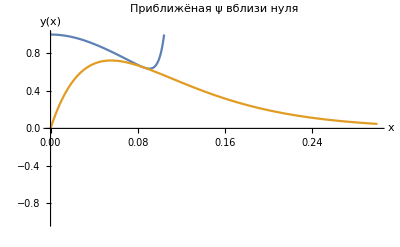

```mathematica
Plot[{PsiSeriesZero[x, 18, 18, 0.078], PsiAway[x, 18, 18, 35.40427175034698]},{x,0,0.3},PlotLabel->"Приближёная ψ вблизи нуля",AxesLabel->{"x","y(x)"},PlotRange->{-1,1}]
```

```mathematica
(*Производные*)
DPsiSeriesZero[x_,z_,k_,a_]=D[PsiSeriesZero[x,z,k,a],x];
DPsiAway[x_,z_,k_,c_]=D[PsiAway[x,z,k,c],x];
```

```mathematica
z0=18;k0=18;a0=0.078;
```

```mathematica
eq1=PsiSeriesZero[x0,z0,k0,a0]==PsiAway[x0,z0,k0,c];
eq2=DPsiSeriesZero[x0,z0,k0,a0]==DPsiAway[x0,z0,k0,c];
```

```mathematica
solution=FindRoot[{eq1,eq2},{{x0,0.09},{c,35}}]
```

{x0→0.0856826,c→35.4043}

```mathematica
x0Fit = x0 /. solution;
cFit = c /. solution;
```

```mathematica
PsiTotal[x_,z_,k_,a_]:=Piecewise[{{PsiSeriesZero[x,z,k,a],x<x0Fit},{PsiAway[x,z,k,cFit],x≥x0Fit}}];
```

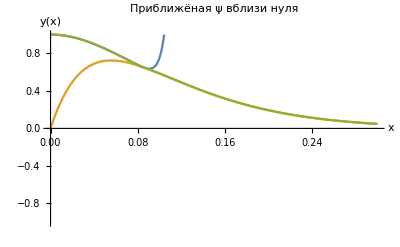

```mathematica
Plot[{PsiSeriesZero[x, 18, 18, 0.078], PsiAway[x, 18, 18, 35.40427175034698], PsiTotal[x, z0, k0, a0]},{x,0,0.3},PlotLabel->"Приближёная ψ вблизи нуля",AxesLabel->{"x","y(x)"},PlotRange->{-1,1}]
```